```mathematica
Map[Contains12,VertexList[MobiusGraph5[K5Key,allGraphs5]]]
```

{True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
VertexList[MobiusGraph5[K5Key,allGraphs5]]
```

{n12x34x5,n12x35x4,n12x3x45,n13x24x5,n13x25x4,n13x2x45,n14x23x5,n14x25x3,n14x2x35,n15x23x4,n15x24x3,n15x2x34,n1x23x45,n1x24x35,n1x25x34,n1x2x3x4x5,n12345,n1234x5,n1235x4,n123x45,n123x4x5,n1245x3,n124x35,n124x3x5,n125x34,n125x3x4,n12x345,n12x3x4x5,n1345x2,n134x25,n134x2x5,n135x24,n135x2x4,n13x245,n13x2x4x5,n145x23,n145x2x3,n14x235,n14x2x3x5,n15x234,n15x2x3x4,n1x2345,n1x234x5,n1x235x4,n1x23x4x5,n1x245x3,n1x24x3x5,n1x25x3x4,n1x2x345,n1x2x34x5,n1x2x35x4,n1x2x3x45}

```mathematica
Table[allGraphs5[k,"colofourrealnull"],{k,allGraphs5NullAtomKeys}]
```

{n1x2x3x4x5,n12x3x4x5,n123x4x5,n1234x5,n12345,n1235x4,n123x45,n124x3x5,n1245x3,n124x35,n125x3x4,n125x34,n12x34x5,n12x345,n12x35x4,n12x3x45,n13x2x4x5,n134x2x5,n1345x2,n134x25,n135x2x4,n135x24,n13x24x5,n13x245,n13x25x4,n13x2x45,n14x2x3x5,n145x2x3,n145x23,n14x23x5,n14x235,n14x25x3,n14x2x35,n15x2x3x4,n15x23x4,n15x234,n15x24x3,n15x2x34,n1x23x4x5,n1x234x5,n1x2345,n1x235x4,n1x23x45,n1x24x3x5,n1x245x3,n1x24x35,n1x25x3x4,n1x25x34,n1x2x34x5,n1x2x345,n1x2x35x4,n1x2x3x45}

```mathematica
Contains12[s_,sub_]:=Fold[Or,Map[Length[Intersection[#,sub]]==Length[sub]&,SymbolToSets[s]]]
```

```mathematica
Contains12[n12x34x5]
```

True

```mathematica
Table[With[{s=allGraphs5[k,"colofourrealnull"]},Rotate[If[Contains12[s],Style[s,Red],s],Pi/4]],{k,allGraphs5NullAtomKeys}]
```

{n1x2x3x4x5,n12x3x4x5,n123x4x5,n1234x5,n12345,n1235x4,n123x45,n124x3x5,n1245x3,n124x35,n125x3x4,n125x34,n12x34x5,n12x345,n12x35x4,n12x3x45,n13x2x4x5,n134x2x5,n1345x2,n134x25,n135x2x4,n135x24,n13x24x5,n13x245,n13x25x4,n13x2x45,n14x2x3x5,n145x2x3,n145x23,n14x23x5,n14x235,n14x25x3,n14x2x35,n15x2x3x4,n15x23x4,n15x234,n15x24x3,n15x2x34,n1x23x4x5,n1x234x5,n1x2345,n1x235x4,n1x23x45,n1x24x3x5,n1x245x3,n1x24x35,n1x25x3x4,n1x25x34,n1x2x34x5,n1x2x345,n1x2x35x4,n1x2x3x45}

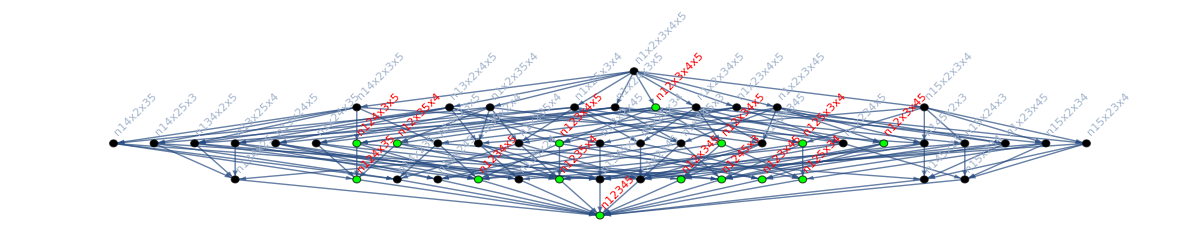

```mathematica
Graph[EdgeList[MobiusGraph5[K5Key,allGraphs5]],  ImageSize->1200, VertexLabels->Table[With[{s=allGraphs5[k,"colofourrealnull"]},s->Rotate[If[Contains12[s,{1,2}],Style[s,Red],s],Pi/4]],{k,allGraphs5NullAtomKeys}],
VertexStyle->Table[With[{s=allGraphs5[k,"colofourrealnull"]},s->If[Contains12[s,{1,2}],Green,Black]],{k,allGraphs5NullAtomKeys}],
GraphLayout->"LayeredDigraphEmbedding"]
```